```mathematica
titiusbode[p_] := With[
{x=PlanetData["Earth","SemimajorAxis"],y=2^(p-1)UnitStep[p-1]},
x(3y+4)/10]
```

```mathematica
belt={"Asteroid Belt",
Mean[LinguisticAssistant]};
```

```mathematica
data=Insert[
MapThread[PlanetData,{{#,#},{"SemimajorAxis","Name"}}]&/@PlanetData[],
{EntityClass["MinorPlanet",#]["SemimajorAxis"]//Mean,#}&@"AsteroidBelt",
 5];
```

```mathematica
prediction=titiusbode/@Range[0,8];
```

```mathematica
AppendTo[data,MinorPlanetData["Pluto",#]&/@{"SemimajorAxis","Name"}];
 (* Since it's not a planet anymore *)
```

```mathematica
names=Last/@data;
distance=First/@data;
```

#### Plot the predicted value vs. actual data

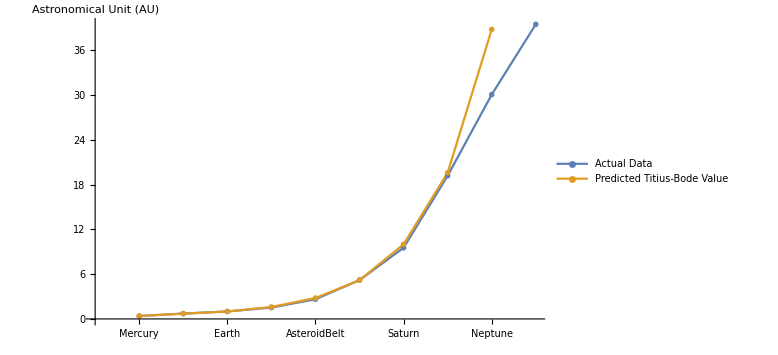

```mathematica
ListPlot[{distance, prediction}, Joined -> True, 
 Ticks -> {Transpose@{Range@Length@names, names}, "Automatic"}, 
 ImageSize -> Large, PlotMarkers -> "OpenMarkers", 
 AxesLabel -> {None, "Astronomical Unit (AU)"}, 
 PlotLegends -> {"Actual Data", "Predicted Titius-Bode Value"}]
```

#### By ignoring the outlaying data!! of Neptune, we see an interesting pattern:

```mathematica
{distance,names}=Transpose@Delete[data,9]; (* delete neptune *)
```

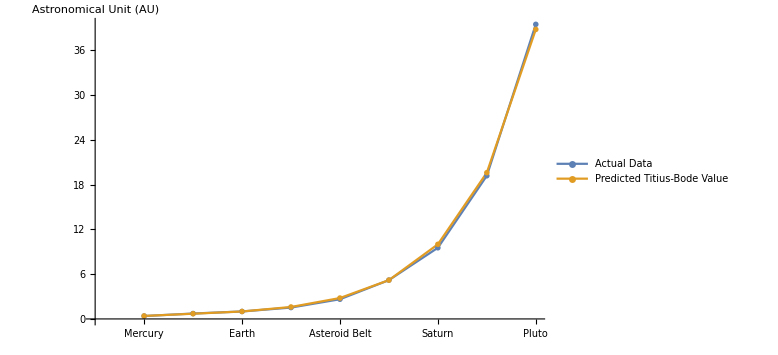

```mathematica
ListPlot[{distance, prediction}, Joined -> True, 
 Ticks -> {Transpose@{Range@Length@names, names}, "Automatic"}, 
 ImageSize -> Large, PlotMarkers -> "OpenMarkers", 
 AxesLabel -> {None, "Astronomical Unit (AU)"}, 
 PlotLegends -> {"Actual Data", "Predicted Titius-Bode Value"}]
```